# Knockout experiment

```mathematica
c=299792458;
u = 931.494;
mp=938.27203;
mn=939.56536;
md=1875.612793;
mHe4=3728.401;
mB11=10255.1;
mC12=11178;
mN13=12114.77;
mN21=19586.63;
mO13=12132.54;
mO14=13048.92;
mO21=19569.44;
mO22=20502.15;
mO23=21438.98;
mO24=22374.93;
mF23=21427.69;
mF24=22363.42;
mF25 = 23298.6337;
massList={mp->"π",mn->"μ",md->"D",mHe4->"α",mB11->"B11",mC12->"C12",mN13->"N13",mN21->"N21",mO13->"O13",mO14->"O14",mO21->"O21",mO22->"O22",mF23-> "F23", mF25->"F25"};
```

```mathematica
(* Notation *)
(* suffix "L" is Lab frame *)
(* suffix "" is Oxygen frame *)
(* suffix "c" is CM frame *)
(* suffix "X" is experiment *)
```

(* knockout [ mO, mi, mk, TiL, k, θk,ϕk,θNN,ϕNN,S] *)

the reaction in oxygen frame is O(i,12)R

mO = mass of oxygen isoptop
mi = mass of incident particle
mk = mass of knockout particle
TiL = K.E. of mi in Lab frame
k = momentum of mX inside oxygen in Oxygen frame
(θk, ϕk) = angle of mX with mi in oxygen rest frame
(θNN, ϕNN) = angle of m1 with mi in CM frame
S = seperation energy of mX from mO

For 2-D Scattering
T1L = T1L[k,θk,θNN,S]
θ1L = θ1L[k,θk,θNN,S]
T2L = T2L[k,θk,θNN,S]
θ2L = θ2L[k,θk,θNN,S]

or 

S = S[T1L,θ1L,T2L,θ2L]
k = k[T1L,θ1L,T2L,θ2L]
θk = θk[T1L,θ1L,T2L,θ2L]
θNN = θNN[T1L,θ1L,T2L,θ2L]

(* coordinate *)
the oxygen is comming from z to 0
using absolute coordinate, which mean, in any frame, the axes are the same.

## Some theory (text)

In the oxygen frame, the proton is coming at 250MeV. After the knockout of a neutron, the residual nucleus is in excited state. We assume the lockout process does not change the energy level of the oxygen nucleus but just leave a hole. If we notate the reaction as , we have 5 4-momentums and the conservation law is: 
P_i+P_O==P_1+P_2+P_R
we have information of the incident proton,the oxygen,the scattered proton and locked out neutron.The missing information is the residual.The excited residual mass pulse the neutron mass and the Separation energy (or the knockout energy,which is the minimum energy that required for knockout process or equivalent as the energy to bring out the orbital neutron to free) should be equal to the oxygen mass.
M_R^*+m_n-S_n==M_O
or
S_n==M_R^*+m_n-M_O=E_x-Q
the Q-factor of the reaction:
Q=m_i+M_O-m_1-m_2-M_R

the conservation laws are:
P_i+P_O==P_1+P_2+P_R
the energy:
E_i+M_O=E_1+E_2+E_R
the momentum :
p_i=p_1+p_2+k
where k is the residual recoil momentmum

Rearrage the equations:
E_i+(M_O-E_R)=E_1+E_2
and:
p_i+(-k)=p_1+p_2
then setting

ℙ_i+ℙ_n=ℙ_1+ℙ_2
E_R^2=M_R^(*2)+k^2
M_R^*=M_0-m_n+S

## Functions

```mathematica
(* all angel in radian, except for display *)
```

### Titled Lorentz Transfrom

The Lorentz Tranform on aribtary direction is well discrpted in Goldstien P .281

```mathematica
(* basis right-hand rotation operator *)
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
(* coordinate transform *)
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[-ϕ].Ry[-θ].Lz[β].Ry[θ].Rz[ϕ]
L[β,θ,ϕ]//FullSimplify//MatrixForm
```

(1/(√(1-β^2)) | (β Cos[ϕ] Sin[θ])/(√(1-β^2)) | (β Sin[θ] Sin[ϕ])/(√(1-β^2)) | (β Cos[θ])/(√(1-β^2))
(β Cos[ϕ] Sin[θ])/(√(1-β^2)) | Cos[ϕ]^2 (Cos[θ]^2+Sin[θ]^2/(√(1-β^2)))+Sin[ϕ]^2 | Cos[ϕ] (-1+Cos[θ]^2+Sin[θ]^2/(√(1-β^2))) Sin[ϕ] | (-1+1/(√(1-β^2))) Cos[θ] Cos[ϕ] Sin[θ]
(β Sin[θ] Sin[ϕ])/(√(1-β^2)) | Cos[ϕ] (-1+Cos[θ]^2+Sin[θ]^2/(√(1-β^2))) Sin[ϕ] | Cos[ϕ]^2+(Cos[θ]^2+Sin[θ]^2/(√(1-β^2))) Sin[ϕ]^2 | (-1+1/(√(1-β^2))) Cos[θ] Sin[θ] Sin[ϕ]
(β Cos[θ])/(√(1-β^2)) | (-1+1/(√(1-β^2))) Cos[θ] Cos[ϕ] Sin[θ] | (-1+1/(√(1-β^2))) Cos[θ] Sin[θ] Sin[ϕ] | Cos[θ]^2/(√(1-β^2))+Sin[θ]^2)

```mathematica
(* Compare the Golsteinn *)
{{γ, -γ βx, -γ βy, γβz},
{-γ βx, 1+(γ-1)βx^2/β^2, (γ-1) (βx βy)/β^2, (γ-1) (βx βz)/β^2},
{-γ βy, (γ-1) (βy βx)/β^2,1+(γ-1)βy^2/β^2, (γ-1) (βy βz)/β^2},
{-γ βz,(γ-1) (βz βx)/β^2, (γ-1) (βy βz)/β^2,1+(γ-1)βz^2/β^2}}//MatrixForm
```

### Rotation on (θ, ϕ) from Left Side

```mathematica
R[ϕNN_,θ_,ϕ_]:=Rz[-ϕ].Ry[-θ].Rz[ϕNN].Ry[θ].Rz[ϕ];
R[α,θ,ϕ]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[ϕ]^2 (Cos[α] Cos[θ]^2+Sin[θ]^2)+Cos[α] Sin[ϕ]^2 | Cos[θ] Sin[α]+Sin[α/2]^2 Sin[θ]^2 Sin[2 ϕ] | -Sin[θ] ((-1+Cos[α]) Cos[θ] Cos[ϕ]+Sin[α] Sin[ϕ])
0 | -Cos[θ] Sin[α]+Sin[α/2]^2 Sin[θ]^2 Sin[2 ϕ] | Cos[α] Cos[ϕ]^2+(Cos[α] Cos[θ]^2+Sin[θ]^2) Sin[ϕ]^2 | Sin[θ] (Cos[ϕ] Sin[α]-(-1+Cos[α]) Cos[θ] Sin[ϕ])
0 | Cos[ϕ] Sin[α/2]^2 Sin[2 θ]+Sin[α] Sin[θ] Sin[ϕ] | -Sin[θ] (Cos[ϕ] Sin[α]+(-1+Cos[α]) Cos[θ] Sin[ϕ]) | Cos[θ]^2+Cos[α] Sin[θ]^2)

```mathematica
Manipulate[Graphics3D[{
{Gray,Line[{{0,0,0},{1,0,0}}]},
Text["x",{1,0,0}],
{Gray,Line[{{0,0,0},{0,1,0}}]},
Text["y",{0,1,0}],
{Gray,Line[{{0,0,0},{0,0,1}}]},
Text["z",{0,0,1}],
{Red,Arrow[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]},
{Blue,Arrow[{{0,0,0},{Cos[θNN] Cos[ϕ] Sin[θ]+Sin[θNN] (Cos[θ] Cos[ϕ] Cos[ϕNN]-Sin[ϕ] Sin[ϕNN]),Cos[θNN] Sin[θ] Sin[ϕ]+Sin[θNN] (Cos[θ] Cos[ϕNN] Sin[ϕ]+Cos[ϕ] Sin[ϕNN]),Cos[θ] Cos[θNN]-Cos[ϕNN] Sin[θ] Sin[θNN]}}]}
},PlotRange->1,ViewPoint->{15,10,7}],{θ,0,π},{ϕ,0,2π},{θNN,0,π},{ϕNN,0,2π}]
```

### basic convertors

```mathematica
Mass[E_,k_]:=√(E^2-k^2);
Momentum[A_]:=√(A[[2]]^2+A[[3]]^2+A[[4]]^2);
k2T[k_,m_]:=√(m^2+k^2)-m;
KE[A_,m_]:=A[[1]]-m
T2k[T_,m_]:=√(2m T+T^2);
Angle[A_]:=If[A[[2]]==0 && A[[3]]==0,{0,0},{ArcTan[A[[4]],√(A[[2]]^2+A[[3]]^2)],ArcTan[A[[2]],A[[3]]]}];
(* angle between 2 vector*)
ΔAngle[A_,B_]:=ArcCos[(A[[2]]B[[2]]+A[[3]]B[[3]]+A[[4]]B[[4]])/(Momentum[A]Momentum[B])];
(* Display DisVector *)
DisVector[A_,name_]:={name,A[[1]],A[[2]],A[[3]],A[[4]]}
(* display (K.E. , momentum, angle 0 *)
β[A_]:=Momentum[A]/A[[1]]
DisEnergy[A_,m_,name_]:={name,A[[1]]-m,Momentum[A],Angle[A][[1]] 180/π,Angle[A][[2]] 180/π}
DscFactor[A_,β_](* Lab to other frame by Lorentz beta *):=Momentum[A]^2/Momentum[(Lz[β].A)]^2(Cos[Angle[A][[1]]]Cos[Angle[Lz[β].A][[1]]]+1/(√(1-β^2))Sin[Angle[A][[1]]]Sin[Angle[Lz[β].A][[1]]]);
```

```mathematica
PX[EX_,kX_,θX_,ϕX_]:={EX,kX Sin[θX]Cos[ϕX],kX Sin[θX]Sin[ϕX],kX Cos[θX]};
P[T_,m_,θ_,ϕ_]:={m+T,T2k[T,m]Sin[θ] Cos[ϕ],T2k[T,m] Sin[θ]Sin[ϕ],T2k[T,m] Cos[θ]};
```

#### Differential Cross Section frame ransform

```mathematica
Manipulate[Plot[1/DscFactor[{√(mp^2+p^2),p Sin[θ °],0,p Cos[θ °]},β],{θ,0,180},GridLines->Automatic],{β,0,1},{p,100,900}]
```

```mathematica
Manipulate[Plot[Cos[ΔAngle[{√(1+p^2),p Sin[θ °],0,p Cos[θ °]},Lz[p/(√(1+p^2))].{√(1+p^2),p Sin[θ °],0,p Cos[θ °]}]],{θ,0,180},GridLines->Automatic],{β,0,1},{p,0.1,3}]
```

```mathematica
Manipulate[Plot[{Momentum[{√(1+p^2),p Sin[θ °],0,p Cos[θ °]}],Momentum[Lz[p/(√(1+p^2))].{√(1+p^2),p Sin[θ °],0,p Cos[θ °]}]},{θ,0,180},GridLines->Automatic],{β,0,1},{p,0.1,3}]
```

```mathematica
Manipulate[Plot[{(Angle[{√(1+p^2),p Sin[θ °],0,p Cos[θ °]}][[1]])*180/π,(Angle[Lz[p/(√(1+p^2))].{√(1+p^2),p Sin[θ °],0,p Cos[θ °]}][[1]])*180/π},{θ,0,180},GridLines->Automatic],{β,0,1},{p,0.1,3}]
```

### Experiment

```mathematica
(* X is form experiment, it generate PnXL = k, θk, SnX = Sn and Subscript[θ, NN] *)
(* given lab frame information, calculated the CM frame *)
(* mi(mO,mR mX) mi *)
X[T1L_,θ1L_,ϕ1L_,T2L_,θ2L_,ϕ2L_,mi_,mO_,mR_,mX_(*the knockout neutron*) ,TiL_]:=
{
PIXL=PX[mi,0,0,0];
P1XL=P[T1L,mi,θ1L,ϕ1L];
P2XL=P[T2L,mX,θ2L,ϕ2L];
βX=(√(2 mi TiL+TiL^2))/(mi+TiL);
(* change to Nucleus frame *)
PIX=PIXL.L[βX,0,0];
P1X=P1XL.L[βX,0,0];
P2X=P2XL.L[βX,0,0];
PnX=Chop[-PIX+P1X+P2X];
PnXL=PnX.L[-βX,0,0];
POX=PX[mO,0,0,0];
POXL=POX.L[-βX,0,0];
Momentum[PnX],
Angle[PnXL][[1]] 180/π,
SnX=√((PIX[[1]]+mO-P1X[[1]]-P2X[[1]])^2-Momentum[PIX-P1X-P2X]^2)-(mO-mX),
Ex=mO-mR-mX+SnX;
PcX=(P1X+P2X)/2;
βPcX=β[PcX];
{θPcX,ϕPcX}=Angle[PcX];
(* in CM frame of a X *)
PcXc=PcX.L[-βPcX,θPcX,ϕPcX];
PIXc=PIX.L[-βPcX,θPcX,ϕPcX];
PnXc=PnX.L[-βPcX,θPcX,ϕPcX];
P1Xc=P1X.L[-βPcX,θPcX,ϕPcX];
P2Xc=P2X.L[-βPcX,θPcX,ϕPcX];
θNNX=ΔAngle[PIXc,P1Xc] 180/π,
SnXL=√((POXL[[1]]+PIXL[[1]]-P1XL[[1]]-P2XL[[1]])^2-Momentum[POXL-P1XL-P2XL]^2)-mO+mX,
γX=1/(√(1-βX^2));
SXonline=(mi-γX mX)-γX(T1L+T2L)+γX βX(Abs[P1XL[[4]]]+Abs[P2XL[[4]]])
}
```

### Experiment Online analysis code

```mathematica
(* X is form experiment, it generate PnXL = k, θk, SnX = Sn and Subscript[θ, NN] *)
(* given lab frame information, calculated the CM frame *)
XOnline[T1L_,θ1L_,ϕ1L_,T2L_,θ2L_,ϕ2L_,mi_,mO_,mR_,mX_(*the knockout neutron*) ,TiL_]:=
{
PIXL=PX[mi,0,0,0];
P1XL=P[T1L,mi,θ1L,ϕ1L];
P2XL=P[T2L,mX,θ2L,ϕ2L];
βX=(√(2 mi TiL+TiL^2))/(mi+TiL);
(* change to Oxygen frame *)
PIX=PIXL.L[βX,0,0];
P1X=P1XL.L[βX,0,0];
P2X=P2XL.L[βX,0,0];
PnX=Chop[-PIX+P1X+P2X];
PnXL=PnX.L[-βX,0,0];
Momentum[PnX],
Angle[PnXL][[1]] 180/π,
SnX=√((PIX[[1]]+mO-P1X[[1]]-P2X[[1]])^2-Momentum[PIX-P1X-P2X]^2)-(mO-mX),
SnOnlineX=mi-1/(√(1-βX^2)) mX-(1/(√(1-βX^2)) (T1L+T2L)- βX/(√(1-βX^2)) (P1XL[[4]]+P2XL[[4]])),
Ex=mO-mR-mX+SnX;
PcX=(P1X+P2X)/2;
βPcX=β[PcX];
{θPcX,ϕPcX}=Angle[PcX];
(* in CM frame of a X *)
PcXc=PcX.L[-βPcX,θPcX,ϕPcX];
PIXc=PIX.L[-βPcX,θPcX,ϕPcX];
PnXc=PnX.L[-βPcX,θPcX,ϕPcX];
P1Xc=P1X.L[-βPcX,θPcX,ϕPcX];
P2Xc=P2X.L[-βPcX,θPcX,ϕPcX];
θNNX=ΔAngle[PIXc,P1Xc] 180/π
}
```

### Simulation

```mathematica
knockout[k_,θk_,ϕk_,θNN_,ϕNN_,S_,mO_,mi_,m_,TiL_]:={
PI=PX[mi+TiL,√(2mi TiL+TiL^2),0,0];
Pn=PX[mO-√((mO-m+S)^2+k^2),k,θk,ϕk]; (* fake 4 vector, for construct the CM frame of a-X*)
Pc=(PI+Pn)/2;
βPc=β[Pc];
{θPc,ϕPc}=Angle[Pc];
(* in CM frame of a X *)
Pcc=Pc.L[-βPc,θPc,ϕPc];
PIc=PI.L[-βPc,θPc,ϕPc];
Pnc=Pn.L[-βPc,θPc,ϕPc];
{θIc,ϕIc}=Angle[PIc];
Etotal=√(1-βPc^2)(PI[[1]]+Pn[[1]]); (* total energy of E1c and E2c *)
k1c=1/(2 Etotal)(√((Etotal-mi-m)(Etotal+mi-m) (Etotal-mi+m) (Etotal+mi+m)));
P1c={√(mi^2+k1c^2),k1c Sin[θIc+θNN]Cos[ϕIc],k1c Sin[θIc+θNN]Sin[ϕIc], k1c Cos[θIc+θNN]}.R[ϕNN,θIc,ϕIc];
P2c={√(m^2+k1c^2) ,k1c Sin[θIc+θNN+π]Cos[ϕIc],k1c Sin[θIc+θNN+π]Sin[ϕIc], k1c Cos[θIc+θNN+π]}.R[ϕNN,θIc,ϕIc];
P1=P1c.L[βPc,θPc,ϕPc];
P2=P2c.L[βPc,θPc,ϕPc];
βPI=β[PI];
PIL=PI.L[-βPI,0,0];
PnL=Pn.L[-βPI,0,0];
P1L=P1.L[-βPI,0,0];
P2L=P2.L[-βPI,0,0];
SnOnline=mi-1/(√(1-βPI^2)) m-(1/(√(1-βPI^2)) (P1L[[1]]-mi+P2L[[1]]-m)- βPI/(√(1-βPI^2)) (Abs[P1L[[4]]+P2L[[4]]]));
Sn=√((PI[[1]]+mO-P1[[1]]-P2[[1]])^2-Momentum[PI-P1-P2]^2)-(mO-m);
(* output *)
P1L,P2L
}
```

## From Experiment

### Numerical Check

```mathematica
(* Generate Possible (p,pn) scattering *)
Manipulate[
knockout[k,θk °,ϕX °,θNN °,ϕNN °,S,mO,m1,m2,TiL];
NumberForm[TableForm[Chop[{
DisVector[P1L,"P1L"],
Temp1=DisEnergy[P1L,m1,"P1L energy"],
DisVector[P2L,"P2L"],
Temp2=DisEnergy[P2L,m2,"P2L energy"],
"",
{"Sp Online",(1-((mp+TiL)/mp))mp-((mp+TiL)/mp)(P1L[[1]]-m1+P2L[[1]]-m2)+((mp+TiL)/mp)√(1-(mp/(mp+TiL))^2)(Abs[P1L[[4]]]+Abs[P2L[[4]]])}
}]],6]
,{{m1,mp},{mp->"π",mn->"μ"}},{{m2,mp},{mp->"π",mn->"μ"}},{{mO,mO14},massList},
{{TiL,247.04},0,1000},{{k,100},0,100},{{θk,90},-180,180},{{ϕX,0},0,360},{{θNN,90},0,180},{{ϕNN,0},0,360},{{S,4.627},0,30},ControlPlacement->Left]
```

```mathematica
Manipulate[
X[T1X,θ1X °,ϕ1X °,T2X,θ2X °,ϕ2X °,m1,mO,mR,m2,TiL];
NumberForm[TableForm[Chop[{
Temp1,
Temp2,
"",
DisVector[POXL,"POXL"],
DisEnergy[POXL,mO,"=POXL energy"],
DisVector[PIXL,"PIXL"],
DisVector[PnXL,"PnXL"],
DisVector[P1XL,"P1XL"],
DisEnergy[P1XL,m1,"=P1XL energy"],
DisVector[P2XL,"P2XL"],
DisEnergy[P2XL,m1,"=P2XL energy"],
DisVector[PIXL+PnXL-P1XL-P2XL," check:"],
DisVector[POXL+PIXL-P1XL-P2XL," POXL+PIXL-P1XL-P2XL"],
DisVector[POXL-P1XL-P2XL," POXL-P1XL-P2XL"],
{"mass of Residual",mR ,Mass[(POXL+PIXL-P1XL-P2XL)[[1]],Momentum[POXL+PIXL-P1XL-P2XL]] },
{"mass of Incident",mO  ,"mass of knockout",m2,mO-m2},
" ",
DisVector[PIX,"PIX"],
DisEnergy[PIX,m1,"=    PIX en"],
DisVector[PnX,"PnX"],
DisEnergy[PnX,m2,"=         k"],
DisVector[P1X,"P1X"],
DisEnergy[P1X,m1,"=P1X energy"],
DisVector[P2X,"P2X"],
DisEnergy[P2X,m2,"=P2X energy"],
{"Sn",SnX,"Ex",Ex},
{"SnL",SnXL,"SXonline",SXonline},
"",
DisVector[PIXc,"PIXc"],
DisVector[PnXc,"PnXc"],
DisVector[P1Xc,"P1Xc"],
DisEnergy[P1Xc,m1,""],
DisVector[P2Xc,"P2Xc"],
DisEnergy[P2Xc,m2,""],
{"θNN",θNNX}
}]],6]
,{{m1,mp},{mp->"π",mn->"μ"}},{{m2,mp},{mp->"π",mn->"μ"}},{{mO,mO14},massList},{{mR,mN13},massList},{{TiL,247.04},0,1000},{{T1X,Temp1[[2]]},0,250},{{θ1X,Temp1[[4]]},0,180},{{ϕ1X,Temp1[[5]]},0,360},{{T2X,Temp2[[2]]},0,250},{{θ2X,Temp2[[4]]},0,180},{{ϕ2X,Temp2[[5]]},0,180},ControlPlacement->Left]
```

### Vector Diagram

```mathematica
Manipulate[
{X[T1X,θ1X π/180,0,T2X,θ2X π/180,π,mp,mO22,mO21,mn,250];
GraphicsRow[
{Graphics[
{
{Black,Arrow[{{PIX[[2]],PIX[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1XL[[2]],P1XL[[4]]}}]},
{Red,Arrow[{{0,0},{P2XL[[2]],P2XL[[4]]}}]},
{Orange,Arrow[{{-PnXL[[2]],-PnXL[[4]]},{0,0}}]}
},PlotRange->1000,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab, Sn="<>ToString[SnX],Epilog->{}],
Graphics[
{
{Purple,Arrow[{{-PIX[[2]],-PIX[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1X[[2]],P1X[[4]]}}]},
{Red,Arrow[{{0,0},{P2X[[2]],P2X[[4]]}}]},
{Green,Arrow[{{0,0},{PcX[[2]],PcX[[4]]}}]},
{Orange,Arrow[{{-PnX[[2]],-PnX[[4]]},{0,0}}]}
},PlotRange->1000,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Oxygen, k="<>ToString[Momentum[PnX]]<>", θ_k="<>ToString[180-Angle[PnX][[1]] 180/π]],
Graphics[
{
{Purple,Arrow[{{-PIXc[[2]],-PIXc[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1Xc[[2]],P1Xc[[4]]}}]},
{Red,Arrow[{{0,0},{P2Xc[[2]],P2Xc[[4]]}}]},
{Orange,Arrow[{{-PnXc[[2]],-PnXc[[4]]},{0,0}}]}
},PlotRange->1000,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Oxygen, k="<>ToString[Momentum[PnX]]<>", θ_k="<>ToString[180-Angle[PnX][[1]] 180/π]
]
},ImageSize-> {1000}]
}
,{{T1X,99},0,250},{{θ1X,160},0,180},{{T2X,6},0,250},{{θ2X,140},0,180}(*,ControlPlacement->Left*)]
```

## Form Simulation

### Numerical Check

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mO,mp,mn,TiL];NumberForm[TableForm[Chop[{
"Setting",{"k",k,"θk, ϕk",θk  °,ϕk  °},{"S",S,"θNN, ϕNN",θNN  °,ϕNN  °},
{"Lab frame", "----", "----", "----"},DisVector[PIL,"PIL"],DisVector[PnL,"PnL"],DisVector[P1L,"P1L"],DisVector[P2L,"P2L"],"",
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1L,mp,"P1L"] ,DisEnergy[P2L,mn,"P2L"],{"β1" , β[P1L]},{"β2" , β[P2L]},(2π-Angle[P1L]-Angle[P2L])180/π,
{"O frame ", "----", "----", "----"},DisVector[PI,"PI"],DisVector[Pn,"Pn"],DisEnergy[Pn,mn,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-PI-Pn,"Diff"],
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[PIc,"PIc"],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"]
}],TableAlignments->{Right}],6],{{mO,mO14},{mO14,mO22,mO23,mO24}},{{TiL,250},0,280},{{k,80},0,100},{{θk,90},0,360},{{ϕk,0},-180,360},{{S,10},0,30},{{θNN,90},0,360},{{ϕNN,0},0,360},ControlPlacement->Left]
```

### Vector Diagram

#### 2D Check

```mathematica
Manipulate[
knockout[k,θk °,0,θNN °,0,S,mO,mp,mn,TiL];
GraphicsRow[
{Graphics[
{
{Black,Arrow[{{PI[[2]],PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1L[[2]],P1L[[4]]}}]},
{Red,Arrow[{{0,0},{P2L[[2]],P2L[[4]]}}]},
{Orange,Arrow[{{-PnL[[2]],-PnL[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab, S="<>ToString[S]<>", k="<>ToString[k]<>", θ_k="<>ToString[-θk  °]<>", θ_NN="<>ToString[θNN  °],Epilog->{Text["θ1L="<>ToString[180-Angle[P1L][[1]] 180/π]<>",β1="<>ToString[β[P1L]]<>",T="<>ToString[DisEnergy[P1L,mp,""][[2]]],{P1L[[2]],P1L[[4]]-90}],Text["θ2L="<>ToString[180-Angle[P2L][[1]] 180/π]<>",β2="<>ToString[β[P2L]]<>",T="<>ToString[DisEnergy[P2L,mn,""][[2]]],{P2L[[2]],P2L[[4]]-50}],
Text["Oxygen",{PI[[2]]-150,PI[[4]]-100}],Text["Orbital Neutron",{-PnL[[2]]+200,-PnL[[4]]-50}]}
]
,
Graphics[
{
{Purple,Arrow[{{-PI[[2]],-PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Oxygen"
]
,
Graphics[
{
{Purple,Arrow[{{-PIc[[2]],-PIc[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{{-Pnc[[2]],-Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[PIc,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]],{0,500}]}
]}
,ImageSize-> {1000}]
,{{mO,mO14},{mO14,mO22,mO23,mO24}},{{TiL,250},0,280},{{k,80},0,100},{{θk,90},0,180},{{S,10},0,30},{{θNN,90},0,180},ControlPlacement->Top]
```

#### 3D Check

```mathematica
Manipulate[
{knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mO22, mp,mn,250];
GraphicsRow[
{Graphics3D[
{
{Black,Arrow[{{PI[[2]],PI[[3]],PI[[4]]},{0,0,0}}]},
{Blue,Arrow[{{0,0,0},{P1L[[2]],P1L[[3]],P1L[[4]]}}]},
{Red,Arrow[{{0,0,0},{P2L[[2]],P2L[[3]],P2L[[4]]}}]},
{Orange,Arrow[{{-PnL[[2]],-PnL[[3]],-PnL[[4]]},{0,0,0}}]}
},PlotRange->800],
Graphics3D[
{
{Purple,Arrow[{{-PI[[2]],-PI[[3]],-PI[[4]]},{0,0,0}}]},
{Blue,Arrow[{{0,0,0},{P1[[2]],P1[[3]],P1[[4]]}}]},
{Red,Arrow[{{0,0,0},{P2[[2]],P2[[3]],P2[[4]]}}]},
{Green,Arrow[{{0,0,0},{Pc[[2]],Pc[[3]],Pc[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[3]],-Pn[[4]]},{0,0,0}}]}
},PlotRange->800],
Graphics3D[
{
{Purple,Arrow[{{-PIc[[2]],-PIc[[3]],-PIc[[4]]},{0,0,0}}]},
{Blue,Arrow[{{0,0,0},{P1c[[2]],P1c[[3]],P1c[[4]]}}]},
{Red,Arrow[{{0,0,0},{P2c[[2]],P2c[[3]],P2c[[4]]}}]},
{Orange,Arrow[{{-Pnc[[2]],-Pnc[[3]],-Pnc[[4]]},{0,0,0}}]}
},PlotRange->1000(*,ViewPoint->{0,10,0}*)]
},ImageSize-> 800]
}
,{{TiL,250},0,1000},{{k,100},0,200},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,0},0,30},{{θNN,90},0,180},{{ϕNN,0},0,360}]
```

### Check All 2D

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mO,m1,m2,TiL];
TableForm[
{{NumberForm[TableForm[Chop[{
"Setting",{"k",k,"θk, ϕk",θk ,ϕk  },{"S",S,"θNN, ϕNN",θNN ,ϕNN },
{"βPI",βPI},
{"SnOnline", SnOnline},
{"Sn", Sn},
{"Lab frame", "----", "----", "----"},DisVector[PIL,"PIL"],DisVector[PnL,"PnL"],DisVector[P1L,"P1L"],DisVector[P2L,"P2L"],"",
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1L,m1,"P1L"] ,DisEnergy[P2L,m2,"P2L"],{"β1" , β[P1L]},{"β2" , β[P2L]},(2π-Angle[P1L]-Angle[P2L])180/π,
{"O frame ", "----", "----", "----"},DisVector[PI,"PI"],DisVector[Pn,"Pn"],DisEnergy[Pn,m2,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-PI-Pn,"Diff"],
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[PIc,"PIc"],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"]
}],TableAlignments->{Right}],6],
Graphics[{{Black,Arrow[{{PI[[2]],PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1L[[2]],P1L[[4]]}}]},
{Red,Arrow[{{0,0},{P2L[[2]],P2L[[4]]}}]},
{Orange,Arrow[{{-PnL[[2]],-PnL[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab, S="<>ToString[S]<>", k="<>ToString[k]<>", θ_k="<>ToString[θk ]<>"°, θ_NN="<>ToString[θNN ]<>"°, ΣT="<>ToString[DisEnergy[P2L,m2,""][[2]]+DisEnergy[P1L,m1,""][[2]]],Epilog->{Text["θ1L="<>ToString[180-Angle[P1L][[1]] 180/π]<>"\nβ1="<>ToString[β[P1L]]<>"\nT1="<>ToString[DisEnergy[P1L,m1,""][[2]]],{P1L[[2]],P1L[[4]]-90}],Text["θ2L="<>ToString[180-Angle[P2L][[1]] 180/π]<>"\nβ2="<>ToString[β[P2L]]<>"\nT2="<>ToString[DisEnergy[P2L,m2,""][[2]]],{P2L[[2]],P2L[[4]]-90}],
Text["Nucleus",{PI[[2]]+150,PI[[4]]-100}],
Text["Orbital Neutron",{-PnL[[2]]-200,-PnL[[4]]-50}],
Text["ΔAngle="<>ToString[ΔAngle[P1L,P2L] 180/π],{0,-620}]},ImageSize->400],
{Graphics[{{Purple,Arrow[{{-PI[[2]],-PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Nucleus",ImageSize->250]
,
Graphics[{{Purple,Arrow[{{-PIc[[2]],-PIc[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{{-Pnc[[2]],-Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[PIc,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]],{0,500}]},ImageSize->250]
}
}
}]
,{{m1,mp},{mp->"Proton",mn->"Neutron"}},{{m2,mp},{mp->"Proton",mn->"Neutron",mHe4->"alpha"}},{{mO,mO14},massList},{{TiL,247.04},0,300},{{k,100},{0,50,100,150,200,270}},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,10},{14.43,20,30,41.53}},{{θNN,90},-180,180},{{ϕNN,0},-180,360},ControlPlacement->Top]
```

### Monte Carlo

```mathematica
n=600;
kM=Table[RandomReal[{0, 300}],{i,1,n}];
SpM=Table[RandomChoice[{0,0,0,0,0,0,0,3.5,9.5,9.5,9.5,9.5,11.74}+4.627],{i,1,n}];
θkList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕkList=Table[ 2π RandomReal[{0,1}],{i,1,n}];
θNNList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕNNList=Table[2π RandomReal[{0,1}],{i,1,n}];
(* outputList = {P1L, P2L} *)
OutputList=Monitor[Table[knockout[kM[[i]],θkList[[i]] ,ϕkList[[i]] ,θNNList[[i]] ,ϕNNList[[i]],SpM[[i]],mO14,mp,mp,250],{i,1,n}],i];
```

```mathematica
Select[SpM,#>0.1 &]
```

{}

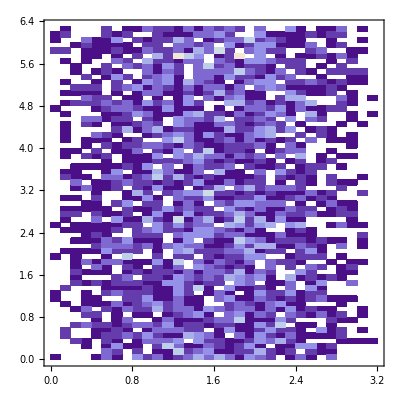

```mathematica
DensityHistogram[
Table[{θkList[[i]],ϕkList[[i]]},{i,1,n}]
,{0.1}]
```

```mathematica
theta1List=Table[Angle[OutputList[[i,1]]] 180/π,{i,1,n}];
theta2List=Table[Angle[OutputList[[i,2]]] 180/π,{i,1,n}];
openning=Flatten[Table[{180-theta1List[[i,1]]+180-theta2List[[i,1]]},{i,1,n}]];
openningPhi=Flatten[Table[{theta1List[[i,2]]-theta2List[[i,2]]},{i,1,n}]];
KE1List=Table[KE[OutputList[[i,1]],mp] ,{i,1,n}];
KE2List=Table[KE[OutputList[[i,2]],mp] ,{i,1,n}];
SumKE=Flatten[Table[{KE1List[[i]]+KE2List[[i]]},{i,1,n}]];
```

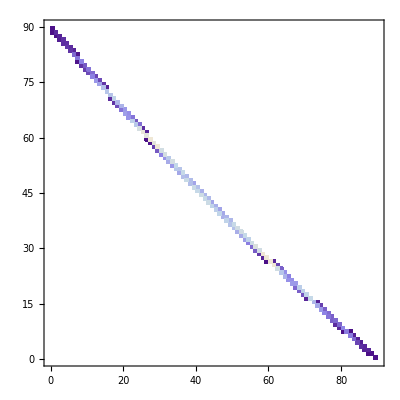

```mathematica
DensityHistogram[
Table[{180-theta1List[[i,1]],180-theta2List[[i,1]]},{i,1,n}]
,{1}]
```

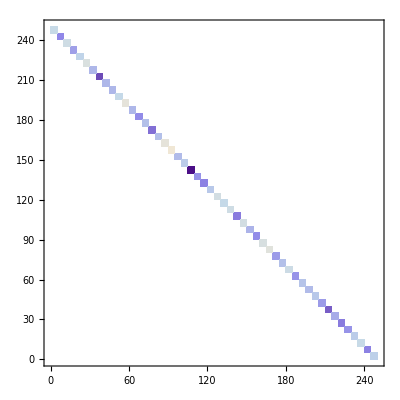

```mathematica
DensityHistogram[
Table[{KE1List[[i]],KE2List[[i]]},{i,1,n}]
,{5}]
```

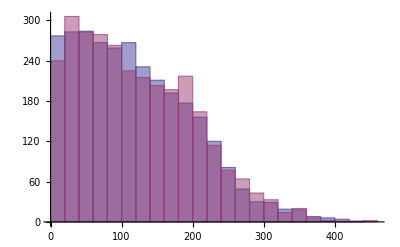

```mathematica
Histogram[
{KE1List,KE2List}
]
```

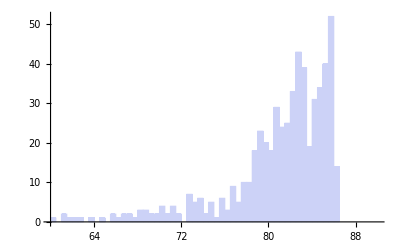

```mathematica
Histogram[
openning
,{60,90,0.5}]
```

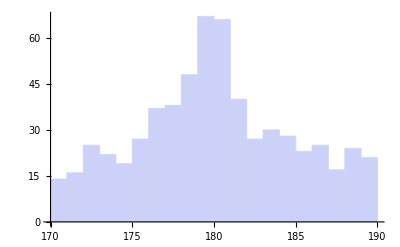

```mathematica
Histogram[
openningPhi
,{170,190,1}]
```

## Some Plots

```mathematica
tF=0.1;
θF=8;
SpList=DeleteCases[Flatten[Table[
J=knockout[k,θk °,0,θNN °,0,Sp,mF23,mp,mp,289];
Sp1=X[KE[J[[1]],mp](1+tF),Angle[J[[1]]][[1]]+θF/1000,Angle[J[[1]]][[2]],KE[J[[2]],mp](1+tF),Angle[J[[2]]][[1]]+θF/1000,Angle[J[[2]]][[2]],mp,mF23,mO22,mp,289][[3]];
Sp2=X[KE[J[[1]],mp](1-tF),Angle[J[[1]]][[1]]-θF/1000,Angle[J[[1]]][[2]],KE[J[[2]],mp](1-tF),Angle[J[[2]]][[1]]-θF/1000,Angle[J[[2]]][[2]],mp,mF23,mO22,mp,289][[3]];
If[{Sp1,Sp2}∈Reals ,{Sp,Sp1,Sp2},{0}],(*{tF,0.01,0.1,0.2},{θF,1,10,1},*){Sp,0,60,1},{k,10,200,10},{θk,10,170,10},{θNN,20,160,10}],3],{0}];
```

```mathematica
testSp1=Table[{SpList[[i,1]],Abs[SpList[[i,2]]-SpList[[i,1]]]},{i,1,Length[SpList]}];
testSp2=Table[{SpList[[i,1]],Abs[SpList[[i,3]]-SpList[[i,1]]]},{i,1,Length[SpList]}];
testSp3=Table[{SpList[[i,1]],√((SpList[[i,2]]-SpList[[i,1]])^2+(SpList[[i,1]]-SpList[[i,3]])^2)},{i,1,Length[SpList]}];
```

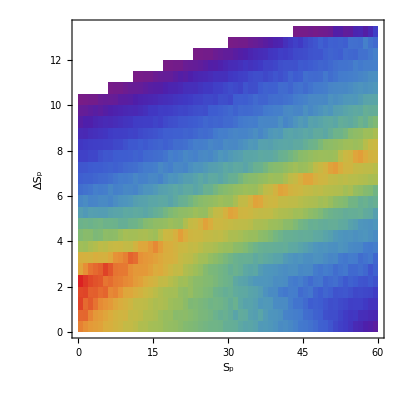

```mathematica
DensityHistogram[testSp1,{{0,60,1},{0,15,0.5}},ColorFunction->Function[{height},ColorData["Rainbow"][height]],Frame->True,FrameLabel->{"S_p", "ΔS_p"}]
```

```mathematica
Histogram3D[testSp1,{{0,30,1},{0,10,0.5}},ChartElementFunction->"GradientScaleCube"]
Histogram3D[testSp2,{{0,30,1},{0,10,0.5}},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

-Graphics3D-

```mathematica
Histogram3D[testSp3,{{0,30,1},{0,10,0.5}},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

### From experiment deduced value (k, θ_k, S_n, θ_NN)plot

```mathematica
Manipulate[
ListPlot[Table[
{T1X,X[T1X,θ1X π/180,0,T2X,θ2X π/180,π,mp,mF23,mO22,mp,289][[A]]},{θ1X,160,110,-10},{T1X,0,250,2}]
,Joined->True,AxesLabel->{"T1X",Which[A==1,"k", A==2, "θk", A==3, "S",A==4, "θNN"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->{600},PlotStyle->{Red,Orange,Brown,Green,Blue,Purple},PlotLabel->"θ_1={20,70,10}, T_2 =" <> ToString[T2X]<>", θ_2 =" <> ToString[θ2X] ]
,{{T2X,125},0,250},{{θ2X,136},90,180},{{A,1,"y-axis"},{1->"k",2->"θk",3->"S",4->" θ_NN"}},ControlPlacement->Left]
```

### Resolution of deduced Value

```mathematica
Manipulate[
ListPlot[Table[
{T1X,X[T1X+Error,π-θ1X π/180,0,T2X,π-θ2X π/180,π,mp,mF23,mO22,mp,289][[A]]},{Error,0,5,5},{T1X,0,250,2}]
,Joined->True,AxesLabel->{"T1X",Which[A==1,"k", A==2, "θk", A==3, "S",A==4, "θNN"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->{600},PlotStyle->{Red,Blue},PlotLabel->"θ_1 ="<>ToString[θ1X]", T_2 =" <> ToString[T2X]<>", θ_2 =" <> ToString[θ2X]]
,{{T2X,125},0,250},{{θ1X,44},0,90},{{θ2X,44},0,90},{{A,1,"y-axis"},{1->"k",2->"θk",3->"S",4->" θ_NN"}},ControlPlacement->Left]
```

```mathematica
Manipulate[
ListPlot[Table[
{X[T1X,π-θ1X π/180,0,T2X,π-θ2X π/180,π,mp,mF23,mO22,mp,289][[3]],1/2(Abs[X[T1X(1+Error),π-θ1X π/180+Error/2 0.001,0,T2X(1+Error),π-θ2X π/180+Error/2 0.001,π,mp,mF23,mO22,mp,289][[A]]-X[T1X,π-θ1X π/180,0,T2X,π-θ2X π/180,π,mp,mF23,mO22,mp,289][[A]]]+Abs[X[T1X(1-Error),π-θ1X π/180-Error/2 0.001,0,T2X(1-Error),π-θ2X π/180-Error/2 0.001,π,mp,mF23,mO22,mp,289][[A]]-X[T1X,π-θ1X π/180,0,T2X,π-θ2X π/180,π,mp,mF23,mO22,mp,289][[A]]])},{θ1X,25,70,15},{T1X,0,200,1}]
,Joined->True,AxesLabel->{"T_1 [MeV]",Which[A==1,"Δk", A==2, "Δθk", A==3, "ΔS",A==4, "ΔθNN"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->{600},PlotStyle->{Red,Orange,Brown,Green,Blue,Purple},PlotLabel->"Resolution of "<>Which[A==1,"k in MeV/c", A==2, "θk in Degree", A==3, "S in MeV",A==4, "θNN in deg"]<>", θ_1={25,70,15}, T_2 =" <> ToString[T2X]<>", θ_2 =" <> ToString[θ2X] <>", ΔT = " <>ToString[Error*100] <>" %"]
,{{T2X,125},0,250},{{θ2X,44},0,90},{{Error,0.05},0,0.2},{{A,3,"y-axis"},{1->"Δk",2->"Δθk",3->"ΔS",4->"ΔθNN"}},ControlPlacement->Left]
```

```mathematica
Manipulate[
ListPlot[Table[
{T1X,Abs[X[T1X,π-θ1X π/180-Error/2 0.001,0,T2X,π-θ2X π/180,π,mp,mF23,mO22,mp,250][[A]]-X[T1X,π-θ1X π/180+Error/2 0.001,0,T2X,π-θ2X π/180,π,mp,mF23,mO22,mp,250][[A]]]},{θ1X,25,70,15},{T1X,0,200,2}]
,Joined->True,AxesLabel->{"T1X [MeV]",Which[A==1,"Δk", A==2, "Δθk", A==3, "ΔS",A==4, "ΔθNN"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->{600},PlotStyle->{Red,Orange,Brown,Green,Blue,Purple},PlotLabel->"Resolution of "<>Which[A==1,"k in MeV/c", A==2, "θk in Degree", A==3, "S in MeV",A==4, "θNN in deg "]<>", θ_1={25,70,15}, T_2 =" <> ToString[T2X]<>", θ_2 =" <> ToString[θ2X] <>", θ1L_Error = " <>ToString[Error] <>" Mrad"]
,{{T2X,125},0,250},{{θ2X,44},0,90},{{Error,10},1,10},{{A,3,"y-axis"},{1->"Δk",2->"Δθk",3->"ΔS",4->"ΔθNN"}},ControlPlacement->Left]
```

### Angle and K.E. in Lab Frame

```mathematica
Manipulate[ListPlot[
Table[knockout[k,θk π/180,0,θNN π/180,ϕNN,S,mO,mp,mk,TiL];
Which[
A== "θ1L vs T1L",{P1L[[1]]-mp,180-Angle[P1L][[1]] 180/π},
A== "θ2L vs T2L",{P2L[[1]]-mn,180-Angle[P2L][[1]] 180/π},
A== "T2L vs T1L",{P1L[[1]]-mp,P2L[[1]]-mn},
A== "θ1L vs θ2L",{180-Angle[P1L][[1]] 180/π,180-Angle[P2L][[1]] 180/π}]
,{S,0,12,3},{θNN,1,181,ΔθNN}],Joined->True,ImageSize->{ 500},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotStyle->{Red, Orange,Green, Blue},AxesLabel->Which[A== "θ1L vs T1L",{"T1L","θ1L"},A== "θ2L vs T2L",{"T2L", " θ2L"},A== "T2L vs T1L",{ "T1L" ,"T2L"},A== "θ1L vs θ2L",{ "θ2L", "θ1L"}],PlotLabel->"S={0, 3, 6, 9,12}, θ_NN={1,180,"<>ToString[ΔθNN]<>"}, k =" <> ToString[k]<>", θ_k =" <> ToString[θk],AspectRatio->If[A== "T2L vs T1L"||A== "θ1L vs θ2L",1,0.6],
PlotRange->If[A== "θ1L vs θ2L",{{0,90},{0,90}},All]],
{{A,"θ1L vs T1L","Set"},{"θ1L vs T1L", "θ2L vs T2L","T2L vs T1L","θ1L vs θ2L"}},{{mO,mF23},massList},{{mk,mp},{mp,mn}},{{TiL,250},{0,100,150,200,250,300}},{{k,100},Table[i ,{i,0,140,10}]},{{θk,90},Table[i , {i,0,180,10}]},{{ϕNN,0},{0,π/3,π/2,2 π/3,π}},{{ΔθNN,5},{1,3,5,10}},ControlPlacement->Left]
```

```mathematica
Manipulate[ListPlot[
{Table[knockout[0,0,0,θNN π/180,0,0,mO,mp,mp,TiL];{θNN,180-Angle[P2L][[1]] 180/π+180-Angle[P1L][[1]] 180/π},{θNN,10,170,1}](*,
Table[knockout[0,0,0,θNN π/180,0,0,mO,mp,mp,TiL];{θNN,180-Angle[P2L][[1]] 180/π},{θNN,0,180,1}],
Table[knockout[0,0,0,θNN π/180,0,0,mO,mp,mp,TiL];{θNN,180-Angle[P1L][[1]] 180/π},{θNN,0,180,1}]*)}
,Joined->True,ImageSize->{ 500},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotStyle->{Red, Orange,Green, Blue}],
{{mO,mO22},{mO14,mO22,mO23,mO24}},{{TiL,300},0,300},ControlPlacement->Left]
```

### Angle vs Momentum in Lab Frame

```mathematica
Manipulate[ListPlot[
Table[knockout[k,θk π/180,0,θNN π/180,0,S,mO,mp,mn,TiL];
Which[
A== "θ1L vs k1",{Momentum[P1L],180-Angle[P1L][[1]] 180/π},
A== "θ2L vs k2",{Momentum[P2L],180-Angle[P2L][[1]] 180/π},
A== "k2 vs k1",{Momentum[P1L],Momentum[P2L]},
A== "θ1L vs θ2L",{180-Angle[P2L][[1]] 180/π,180-Angle[P1L][[1]] 180/π}],{S,2,14,4},{θNN,1,180,2}],Joined->True,ImageSize-> {500},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotStyle->{Red, Orange,Green, Blue},AxesLabel->Which[A== "θ1L vs k1",{"k1","θ1L"},A== "θ2L vs k2",{"k2", " θ2L"},A== "k2 vs k1",{ "k1" ,"k2"},A== "θ1L vs θ2L",{ "θ2L", "θ1L"}],PlotLabel->"S={2, 6, 10, 14}, θ_NN={1,180,2}, k =" <> ToString[k]<>", θ_k =" <> ToString[θk],AspectRatio->If[A== "k2 vs k1"||A== "θ1L vs θ2L",Automatic,0.6]],
{{mO,mO22},{mO14,mO22,mO23,mO24}},{A,{"θ1L vs k1", "θ2L vs k2","k2 vs k1","θ1L vs θ2L"}},{{TiL,250},0,280},{{k,0},0,100},{{θk,90},0,180},ControlPlacement->Left]
```

### 3 D plot for 3 qauntaties

```mathematica
Manipulate[ListPointPlot3D[
Flatten[Table[knockout[k,θk π/180,0,θNN π/180,ϕNN,S,mO,mp,mk,TiL];
Which[
A== "θ1L vs T1L",{P1L[[1]]-mp,180-Angle[P1L][[1]] 180/π,180-Angle[P2L][[1]] 180/π},
A== "θ2L vs T2L",{P2L[[1]]-mn,180-Angle[P2L][[1]] 180/π,k},
A== "T2L vs T1L",{P1L[[1]]-mp,P2L[[1]]-mn,k},
A== "θ1L vs θ2L",{180-Angle[P2L][[1]] 180/π,180-Angle[P1L][[1]] 180/π,k}]
,{θk,0, 180, 10},{S,0,15,5},{θNN,1,179,ΔθNN}],1],ImageSize->{ 500},PlotStyle->{Red, Orange,Green, Blue},AxesLabel->Which[A== "θ1L vs T1L",{"T1L","θ1L","θ2L"},A== "θ2L vs T2L",{"T2L", " θ2L"},A== "T2L vs T1L",{ "T1L" ,"T2L"},A== "θ1L vs θ2L",{ "θ2L", "θ1L"}],PlotLabel->"S={2, 4, 6, 8}, θ_NN={1,180,"<>ToString[ΔθNN]<>"}, k =" <> ToString[k]<>", θ_k =" <> ToString[θk],BoxRatios->1],
{{A,"θ1L vs T1L","Set"},{"θ1L vs T1L", "θ2L vs T2L","T2L vs T1L","θ1L vs θ2L"}},{{mO,mO22},{mO14,mO22,mO23,mO24}},{{mk,mn},{mp,mn}},{{TiL,250},{0,100,150,200,250}},{{k,100},Table[i , {i,0,120,10}]},{{ϕNN,0},{0,π/3,π/2,2 π/3,π}},{{ΔθNN,5},{1,3,5,10}},ControlPlacement->Left]
```

Part::partd: Part specification P1L ⟦ 1 ⟧ is longer than depth of object.

### k-space in Lab Frame

```mathematica
(* Plot the k-space of P1L, P2L *)
Manipulate[ListPlot[
{Table[knockout[k,θk π/180,0,θNN π/180,0,S,mO,mp,mn,TiL];
{Momentum[P1L]Sin[Angle[P1L][[1]]]Cos[Angle[P1L][[2]]],Momentum[P1L]Cos[Angle[P1L][[1]]]},{θNN,0,180,5}],
Table[knockout[k,θk π/180,0,θNN π/180,0,S,mO,mp,mn,TiL];
{Momentum[P2L]Sin[Angle[P2L][[1]]]Cos[Angle[P2L][[2]]],Momentum[P2L]Cos[Angle[P2L][[1]]]},{θNN,0,180,5}]},
(*Joined->True,*)ImageSize-> {500},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],AxesLabel->{"kx","kz"},PlotLabel->"k =" <> ToString[k],AspectRatio->Automatic],
{{mO,mO22},{mO14,mO22,mO23,mO24}},{{TiL,250},0,280},{{k,1},1,100},{{θk,90},1,180},{S,25,70,15}]
```

### T Space in Lab Frame

```mathematica
(* Plot the T-space of P1L, P2L *)
Manipulate[ListPlot[
{Table[knockout[k,θk π/180,0,θNN π/180,0,S,mO,mp,mn,TiL];
{(P1L[[1]]-mp)Sin[Angle[P1L][[1]]]Cos[Angle[P1L][[2]]],(P1L[[1]]-mp)Cos[Angle[P1L][[1]]]},{θNN,1,180,5}],
Table[knockout[k,θk π/180,0,θNN π/180,0,S,mO,mp,mn,TiL];
{(P2L[[1]]-mn)Sin[Angle[P2L][[1]]]Cos[Angle[P2L][[2]]],(P2L[[1]]-mn)Cos[Angle[P2L][[1]]]},{θNN,1,180,5}]},
(*Joined->True,*)ImageSize-> {500},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],AxesLabel->{"Tx","Tz"},PlotLabel->"k =" <> ToString[k],AspectRatio->Automatic],
{{mO,mO22},{mO14,mO22,mO23,mO24}},{{TiL,250},0,280},{{k,1},1,100},{S,25,70,15},{{θk,90},0,180}]
```